## PRAVILNI VEČKOTNIKI IN PLATONSKA TELESA

### Pravilni večkotnik

Pravilni mnogokotnik ali pravilni večkotnik je mnogokotnik, ki ima vse stranice enako dolge in vse kote med seboj skladne. 
Naslednja funkcija skonstruira poljuben mnogokotnik, ki mu podamo število stranic in dolžino ene stranice. S pomočjo teh podatkov lahko izračunamo tudi obseg, število diagonal in velikost notranjih kotov poljubnega mnogokotnika.

```mathematica
Narisi[p__PravilniNKotnik] := Graphics[{
	Line[
		Table[{p[[2]] * Cos[(2*Pi * i) / p[[1]]],
		p[[2]] * Sin[(2*Pi * i) / p[[1]]]}, {i, 0, p[[1]]}]]}]
Obseg[p__PravilniNKotnik] := p[[1]] * p[[2]]
ŠtDiagonal[p__PravilniNKotnik] := p[[1]] * (p[[1]] - 3) / 2
NotranjiKot[p__PravilniNKotnik] := (p[[1]] - 2) * 180 / p[[1]]
```

V nadaljevanju bom predstavila nekaj pravilnih večkotnikov tako, da jih bom narisala, izračunala njihov obseg, število diagonal, velikost notranjih kotov ter višino in ploščino.

#### Enakostranični trikotnik

```mathematica
p3 = PravilniNKotnik[3, 2];
```

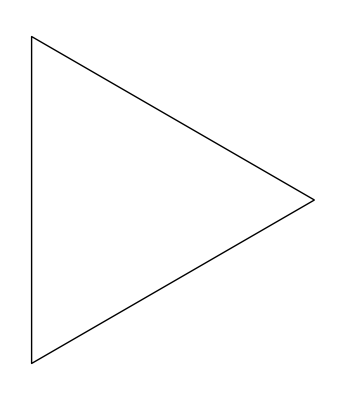

```mathematica
Narisi[p3]
```

```mathematica
Obseg[p3]
```

6

```mathematica
ŠtDiagonal[p3]
```

0

```mathematica
NotranjiKot[p3]
```

60

Poleg zgornjih lastnosti lahko enakostraničnemu trikotniku izračunamo tudi višino, ter s pomočjo višine tudi ploščino trikotnika.

```mathematica
VišinaTrikotnika[p__PravilniNKotnik] := 3^(1/2)/2 * p[[2]]
PloščinaTrikotnika[p__PravilniNKotnik] := VišinaTrikotnika[p]*p[[2]]/2
```

```mathematica
VišinaTrikotnika[p3]
```

√3

```mathematica
PloščinaTrikotnika[p3]
```

√3

#### Kvadrat

```mathematica
p4 = PravilniNKotnik[4, 2];
```

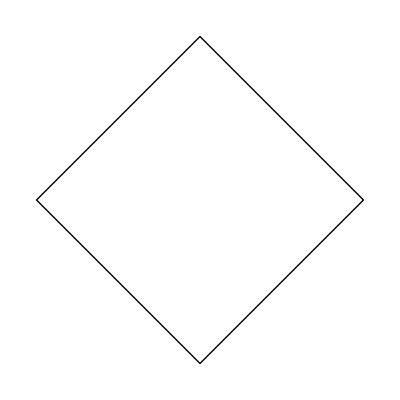

```mathematica
Narisi[p4]
```

```mathematica
Obseg[p4]
```

8

```mathematica
ŠtDiagonal[p4]
```

2

```mathematica
NotranjiKot[p4]
```

90

```mathematica
PloščinaKvadrata[p__PravilniNKotnik] := p[[2]] * p[[2]]
```

```mathematica
PloščinaKvadrata[p4]
```

4

#### Pravilni 5-kotnik

```mathematica
p5 = PravilniNKotnik[5, 2];
```

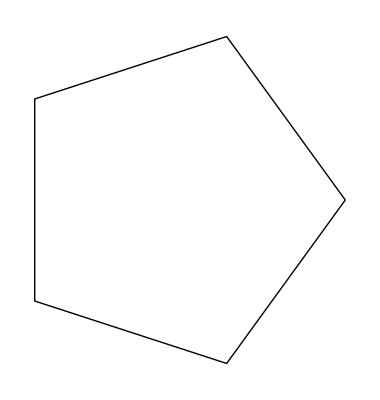

```mathematica
Narisi[p5]
```

```mathematica
Obseg[p5]
```

10

```mathematica
ŠtDiagonal[p5]
```

5

```mathematica
NotranjiKot[p5]
```

108

#### Pravilni n-kotniki

```mathematica
d = 2;
Manipulate[Graphics[{
	Line[
		Table[{d * Cos[(2*Pi * i) / n],
		d * Sin[(2*Pi * i) / n]}, {i, 0, n}]]}], {n, 3, 20, 1}]
```

#### Včrtana in očrtana krožnica

Vsakemu pravilnemu večkotniku lahko včrtamo in očrtamo krožnico. Spodnje funkcije izračunajo polmer očrtane in včrtane krožnice za poljuben večkotnik.

```mathematica
PolmerOčrtane[p__PravilniNKotnik] := p[[2]] / (2*Sin[180 Degree/p[[1]]])
PolmerVčrtane[p__PravilniNKotnik] := p[[2]] / (2*Tan[180 Degree/p[[1]]])
```

```mathematica
PolmerOčrtane[p3]
```

2/(√3)

```mathematica
PolmerOčrtane[p4]
```

√2

```mathematica
PolmerOčrtane[p5]
```

1/(√(5/8-(√5)/8))

```mathematica
PolmerVčrtane[p3]
```

1/(√3)

```mathematica
PolmerVčrtane[p4]
```

1

```mathematica
PolmerVčrtane[p5]
```

1/(√(5-2 √5))

### Platonska telesa

Platonsko telo je telo, katerega stranske ploskve so skladni pravilni mnogokotniki z značilnostjo, da se v vsakem oglišču stika isto število stranskih ploskev. Največja zanimivost Platonskih teles je, da jih obstaja le pet.

#### Tetraeder

Tetraeder je tristrana piramida. Dobimo ga, če skupaj sestavimo štiri enakostranične trikotnike.

```mathematica
Graphics3D[Tetrahedron[{{1,0,0},{1,0,1},{1,1,1},{0,0,1}}]]
```

-Graphics3D-

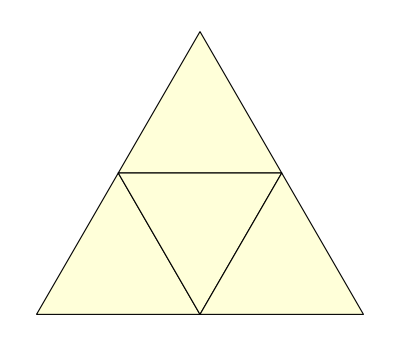

```mathematica
PolyhedronData["Tetrahedron","NetImage"]
```

#### Kocka

Kocka ali heksaeder ima za osnovno ploskev kvadrat. Da lahko sestavimo kocko potrebujemo 6 kvadratov.

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

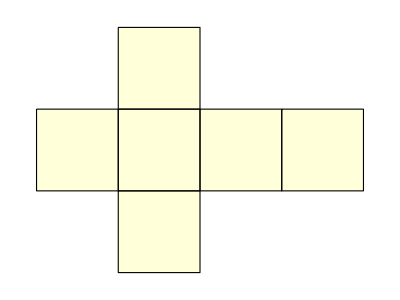

```mathematica
PolyhedronData["Cube","NetImage"]
```

#### Oktaeder

Oktaeder izgleda kot dve tristrani piramidi, ki bi jim eno ploskev prilepili skupaj. Tako da zanj potrebujemo 8 enakostraničnih trikotnikov.

```mathematica
v={{-1, -1, 0}, {-1, 1, 0}, {0, 0, -(1/Sqrt[2])}, 
  {0, 0, 1/Sqrt[2]}, {1, -1, 0}, {1, 1, 0}};
Graphics3D[GraphicsComplex[v,
 Polygon[{{4, 5, 6}, {4,6, 2}, {4, 2, 1}, {4, 1, 5}, {5, 1, 3}, {5, 3, 6}, 
   {3, 1, 2}, {6, 3, 2}}]]]
```

-Graphics3D-

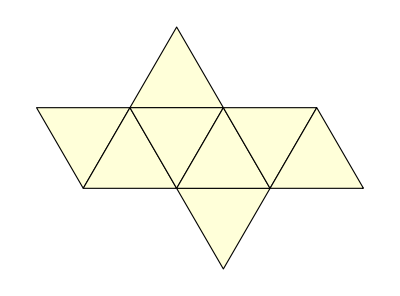

```mathematica
PolyhedronData["Octahedron","NetImage"]
```

#### Ikozaeder

Zanimivo je da največ obstoječih platonskih teles sestavljajo enakostranični trikotniki. Eden izmed teh je tudi ikozaeder, za katerega potrebujemo kar 20 enakostraničnih trikotikov.

```mathematica
PolyhedronData["Icosahedron"]
```

-Graphics3D-

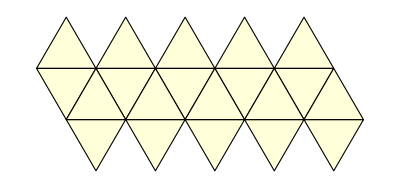

```mathematica
PolyhedronData["Icosahedron","NetImage"]
```

#### Dodekaeder

Poleg trikotnikov in kvadratov pa lahko Platonsko telo sestavimo tudi iz petkotnikov. Tako telo se imenuje dodekaeder in je sestavljen iz dvanajstih petkotnikov.

```mathematica
PolyhedronData["Dodecahedron"]
```

-Graphics3D-

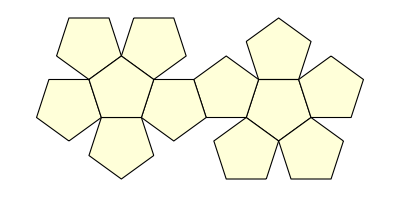

```mathematica
PolyhedronData["Dodecahedron","NetImage"]
```

#### Zakaj samo 5?

Če telo razgrnemo, se pravi ga spravimo iz 3D prostora v dvodimenzionalen prostor, mora biti vsota kotov v istem oglišču manjša od 360°.

Ker se morajo v vsakem oglišču stikati vsaj trije pravilni mnogokotniki, notranji kot večkotnika ne sme presegati 120°.To pomeni, da lahko taka telesa sestavimo le iz enakostraničnih trikotnikov, kvadratov in pravilnih 5-kotnikov.

enakostraničnotrikotniške stranske ploskve : vsako oglišče enakostraničnega trikotnika je 60 °, tako, da ima oblika lahko 3, 4 ali 5 enakostraničnih trikotnikov, ki se stikajo v oglišču.To so tetraeder, oktaeder in ikozaeder

kvadratne stranske ploskve : vsako oglišče kvadrata je 90 °, tako da je možna samo ena postavitev s tremi stranskimi ploskvami v oglišču.To je kocka.

petkotniške stranske ploskve : vsako oglišče petkotnika je 108 °, tako da je možna samo ena postavitev s tremi stranskimi ploskvami v oglišču.To je dodekaeder.

Skupaj je tako možnih le 5 platonskih teles.

#### Ostala telesa iz pravilnih mnogokotnikov

Poleg Platonskih teles, pa lahko iz pravilnih mnogokotnikov sestavimo tudi druga telesa, za katere združimo različne mnogokotnike.

12 petkotnikov in 20 šestkotnikov :

```mathematica
PolyhedronData["TruncatedIcosahedron"]
```

-Graphics3D-

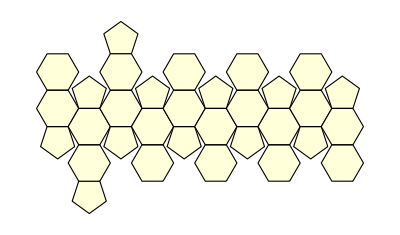

```mathematica
PolyhedronData["TruncatedIcosahedron","NetImage"]
```

6 kvadratov in 32 enakostraničnih trikotnikov

```mathematica
PolyhedronData["SnubCube"]
```

-Graphics3D-

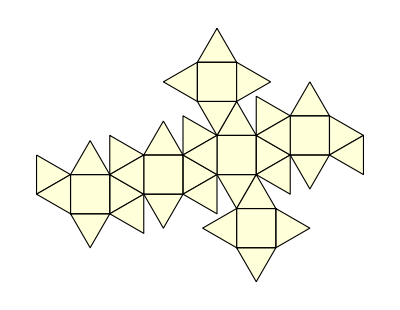

```mathematica
PolyhedronData["SnubCube","NetImage"]
```